```mathematica
u=(0.015625-0.203125 ⅇ^(ⅈ ξ)+0.9375 ⅇ^(2 ⅈ ξ)-1.75 ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(0.52734375-3 d) ⅇ^(ⅈ ξ)+(-1.6875+3 d) ⅇ^(2 ⅈ ξ)+(1.58203125-d) ⅇ^(3 ⅈ ξ));
```

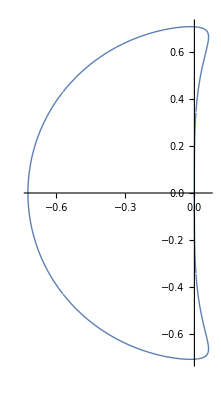

```mathematica
d=-0.2;
p1=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
```

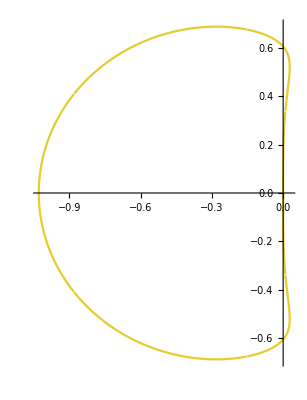

```mathematica
d=0;
p2=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.9,0.8,0.19]
,AxesOrigin->{0,0}
,PlotRange->All]
```

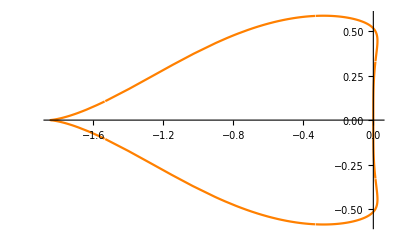

```mathematica
d=0.21;
p3=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Orange
,AxesOrigin->{0,0}
,PlotRange->All]
```

```mathematica
Show[p1,p2,p3]
```

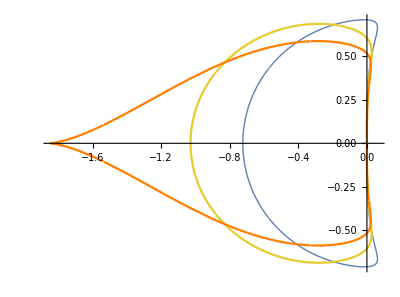

-Graphics-

```mathematica
Show[%14,ImageSize->Large,AxesLabel->{Style[Re Z,Medium],Style[Im Z,Medium]},LabelStyle->{18,GrayLevel[0]}]
```

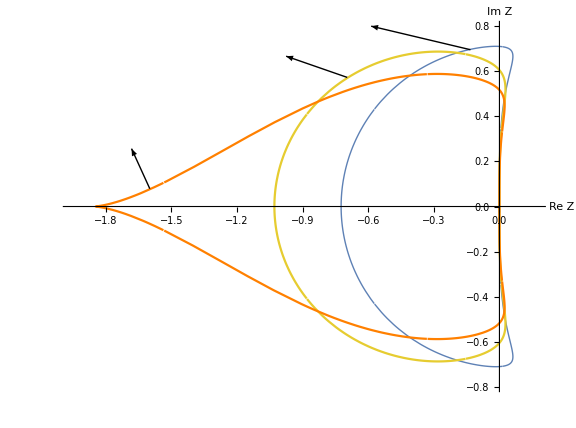

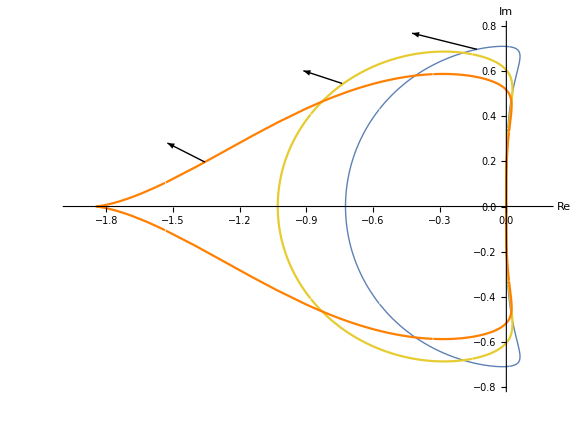

-Graphics-